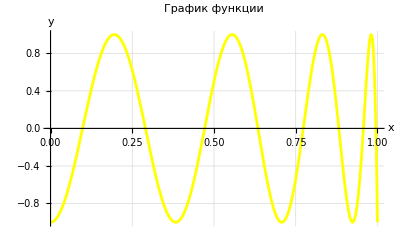

```mathematica
f[x_]:=1-2*x^2
Plot[f[f[f[f[x]]]], {x, 0, 1},PlotLabel->Style["График функции"],AxesLabel->{"x","y"},GridLines->Automatic,PlotStyle->{Yellow}]
```

```mathematica
Plot3D[Sin[x/(y+Pi/10)],{x,0 ,2*Pi}, {y, 0, Pi/2}, PlotPoints->40, AxesLabel->{"X", "Y", "Z"}, ViewPoint->{0, -2, 0}]
```

-Graphics3D-

```mathematica
Solve[Log[x+Sqrt[x^2+a]]==b, x]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→1/2 ⅇ^-b (-a+ⅇ^(2 b))}}

```mathematica
Solve[x^4-5*x^2-3==0, x]
```

{{x→-ⅈ √(1/2 (-5+√37))},{x→ⅈ √(1/2 (-5+√37))},{x→-√(1/2 (5+√37))},{x→√(1/2 (5+√37))}}

```mathematica
Solve[Cos[x]==Tan[x],x]
```

{{x→ConditionalExpression[π-ArcTan[√(1/2 (-1+√5))]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[√(1/2 (-1+√5))]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[-ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[Log[Sqrt[x]]==Sqrt[Log[x]], x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1},{x→ⅇ^4}}

```mathematica
Solve[x^3-3*x-1==0,x]
```

{{x→},{x→},{x→}}

```mathematica
Solve[a*x^4+b*x^3+1==0, x]
```

{{x→-b/(4 a)+1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))-1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)-b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)+1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))+1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)-b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))-1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)+b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))+1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)+b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))}}

```mathematica
NSolve[x^7+7*x==7,x]
```

{{x→-1.3217-0.706695 ⅈ},{x→-1.3217+0.706695 ⅈ},{x→-0.137797-1.43289 ⅈ},{x→-0.137797+1.43289 ⅈ},{x→0.920191},{x→0.999402-0.797172 ⅈ},{x→0.999402+0.797172 ⅈ}}

```mathematica
NSolve[Cos[x]==x, x]
```

{{x→0.739085},{x→-2.48689+1.80936 ⅈ},{x→-9.10999+2.95017 ⅈ},{x→-15.488+3.45661 ⅈ},{x→-21.819+3.79031 ⅈ},{x→-28.1316+4.03995 ⅈ},{x→-34.435+4.23954 ⅈ},{x→-40.7329+4.40585 ⅈ},{x→-47.0274+4.54842 ⅈ},{x→-53.3196+4.67319 ⅈ},{x→-59.6102+4.78411 ⅈ},{x→-65.8995+4.88396 ⅈ},{x→-72.1878+4.97474 ⅈ},{x→-78.4754+5.05797 ⅈ},{x→-84.7625+5.1348 ⅈ},{x→-91.0491+5.20615 ⅈ}}

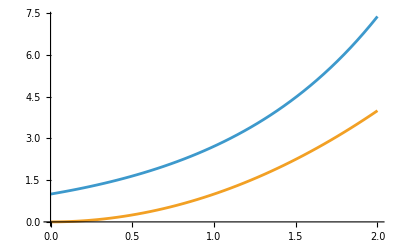

{x→-0.703467}

```mathematica
Plot[{Exp[x],x^2},{x,0,2}]
FindRoot[Exp[x]==x^2, {x, 0.7}]
```

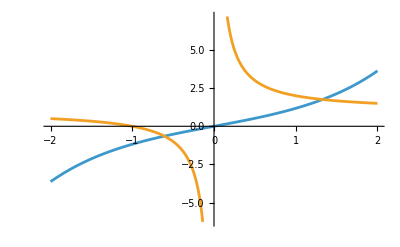

{x→1.32752}

Plot::pllim: Range specification x is not of the form {x, xmin, xmax}.

```mathematica
Plot[{Sinh[x], 1+1/x}, {x,-2,2}]
FindRoot[Sinh[x]==1+1/x, {x,1.3}]
```

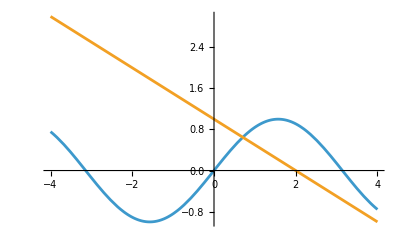

```mathematica
Plot[{Sin[x],1-x/2},{x, -4,4}]
```

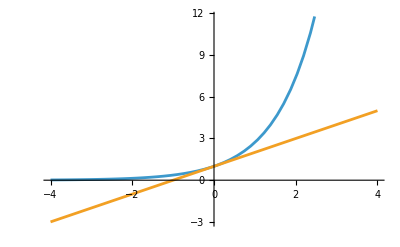

```mathematica
Plot[{Exp[x], x+1}, {x,-4,4}]
```

```mathematica
solution = Solve[{x+y==5,x-y==1}, {x,y}]
{x+y==5, x-y==1}/.solution
```

{{x→3,y→2}}

{{True,True}}

```mathematica
Solve[{Sqrt[x+y]==Sqrt[x*y],x^2+y^2==1}, {x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/2 (1-√2+√(-1+2 √2)),y→1/2 (1-√2-√(-1+2 √2))},{x→1/2 (1-√2-√(-1+2 √2)),y→1/2 (1-√2+√(-1+2 √2))},{x→1/2+1/(√2)+1/2 ⅈ √(1+2 √2),y→1/2+1/(√2)-1/2 ⅈ √(1+2 √2)},{x→1/2+1/(√2)-1/2 ⅈ √(1+2 √2),y→1/2+1/(√2)+1/2 ⅈ √(1+2 √2)}}

```mathematica
Solve[{Sin[x+y]==Cos[x-y],Tan[x*y]==Cos[x*y]},{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(4 ArcCos[-√(1/2 (-1+√5))])/π,y→π/4},{x→(4 ArcCos[√(1/2 (-1+√5))])/π,y→π/4},{x→(4 ArcCos[-ⅈ √(1/2 (1+√5))])/(3 π),y→-(3 π)/4},{x→(4 ArcCos[ⅈ √(1/2 (1+√5))])/(3 π),y→-(3 π)/4},{x→π/4,y→(4 ArcCos[-√(1/2 (-1+√5))])/π},{x→π/4,y→(4 ArcCos[√(1/2 (-1+√5))])/π},{x→-(3 π)/4,y→(4 ArcCos[-ⅈ √(1/2 (1+√5))])/(3 π)},{x→-(3 π)/4,y→(4 ArcCos[ⅈ √(1/2 (1+√5))])/(3 π)}}

```mathematica
Eliminate[{x^2+y^2-z^2==1,x+y==z,Sinh[z]==x^2+y^2},{x,y}]
NSolve[%,z]
```

1+z^2-Sinh[z]==0

{{z→0.473104+0.973506 ⅈ},{z→0.473104-0.973506 ⅈ},{z→2.99559},{z→-4.43723+4.75869 ⅈ},{z→5.25579+8.2847 ⅈ},{z→-4.43723-4.75869 ⅈ},{z→6.2568+14.9106 ⅈ},{z→-5.82085-11.6338 ⅈ},{z→6.91457+21.364 ⅈ},{z→-6.61299-18.149 ⅈ},{z→7.40754+27.7521 ⅈ},{z→-7.17628-24.5634 ⅈ},{z→7.80245+34.1074 ⅈ},{z→-7.61474-30.9327 ⅈ},{z→8.13206+40.4436 ⅈ},{z→-7.97403-37.2774 ⅈ}}

```mathematica
DSolve[y''[x]*x^2+5*y'[x]*x+y[x]==0,y[x],x]
```

{{y[x]→x^(1/2 (-4-2 √3)) C[1]+x^(1/2 (-4+2 √3)) C[2]}}

```mathematica
DSolve[y''[x]*x^2+3*y'[x]*x+y[x]==Sin[2*x],y[x],x]
```

{{y[x]→C[1]/x-CosIntegral[2 x]/(2 x)+(C[2] Log[x])/x}}

```mathematica
DSolve[{y''[x]*x^2+5*y'[x]*x+y[x]==x^(-2+Sqrt[3]),y[1]==-1/12,y'[1]==1/12*(2+Sqrt[3])},y[x],x]
```

{{y[x]→1/12 x^(-2+√3) (-1+2 √3 Log[x])}}

```mathematica
DSolve[y''[x]+y[x]/Sin[x]^2==0,y[x],x]
```

{{y[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[-1/2,(ⅈ √3)/2,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[-1/2,(ⅈ √3)/2,Cos[x]]}}

```mathematica
DSolve[{x'[t]==t^2+y[t],y'[t]==x[t]},{x[t],y[t]},t]
```

{{x[t]→1/4 ⅇ^(-2 t) (-1+ⅇ^(2 t)) (-2-2 t-t^2-ⅇ^(2 t) (2-2 t+t^2))+1/4 ⅇ^(-2 t) (1+ⅇ^(2 t)) (-2-2 t-t^2+ⅇ^(2 t) (2-2 t+t^2))+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y[t]→1/4 ⅇ^(-2 t) (1+ⅇ^(2 t)) (-2-2 t-t^2-ⅇ^(2 t) (2-2 t+t^2))+1/4 ⅇ^(-2 t) (-1+ⅇ^(2 t)) (-2-2 t-t^2+ⅇ^(2 t) (2-2 t+t^2))+1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

```mathematica
DSolve[{y''[t]==4*x[t]-5*y[t],x''[t]==4*y[t]-5*x[t],y[0]==1,x[0]==0,y'[0]==0,x'[0]==1},{x[t],y[t]},t]
```

{{x[t]→1/6 (3 Cos[t]-3 Cos[3 t]+3 Sin[t]+Sin[3 t]),y[t]→1/6 (3 Cos[t]+3 Cos[3 t]+3 Sin[t]-Sin[3 t])}}

{{x[t]→2. JacobiAmplitude[0.9995 t,1.001]}}

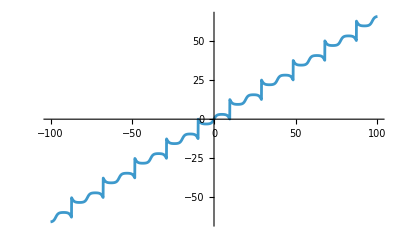

DSolve::dvnoarg: The function y[t] appears with no arguments.

DSolve[{x'[t]==t^2+y[t],y'[t]==x[t]},y[t],x[t]]

```mathematica
DSolve[{x''[t]==-Sin[x[t]],x[0]==0,x'[0]==1.999},x[t],{t,0,20}]
Plot[x[t]/.%,{t,-100,100}]
```